```mathematica
ClearAll["Global`*"]
```

```mathematica
A = {{0 ,0,.5},{.2,0,0},{0,.05,.9}}
A2 = {{0 ,0,0},{.2,0,0},{0,.05,.9}}
gridSizeX = 10
gridSizeY = 10
```

{{0,0,0.5},{0.2,0,0},{0,0.05,0.9}}

{{0,0,0},{0.2,0,0},{0,0.05,0.9}}

10

10

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

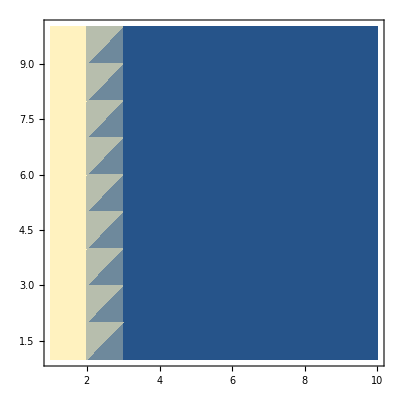

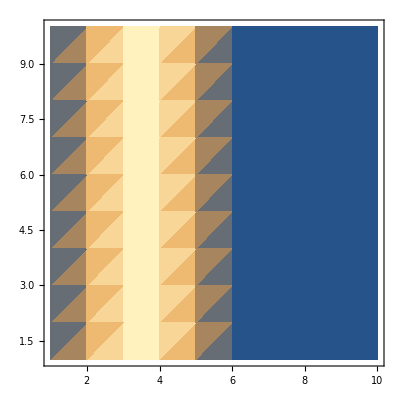

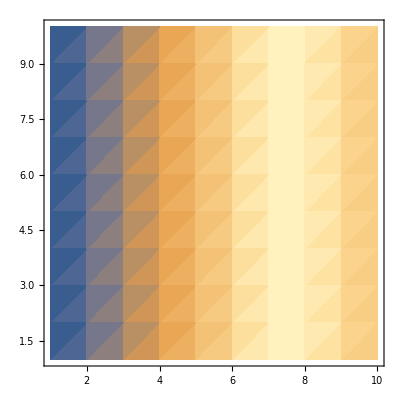

```mathematica
ConstantArray[0,{gridSizeX ,gridSizeY}];
HSI1= ConstantArray[0,{gridSizeX,gridSizeY}];
HSI1[[1;; gridSizeX ,1;;2]]= 1;
HSISTORE[1] = HSI1;
Floor[gridSizeY*.3];
HSI2= ConstantArray[0,{gridSizeX,gridSizeY}];
insert1 = Array[#&,Floor[gridSizeY*.3],{0,2/3}];
insert2 = Array[#&,Floor[gridSizeY*.3],{2/3,0}];
Join[insert1,insert2];
HSI2[[1;; gridSizeX-1 ,1;;2*Floor[gridSizeY*.3]]] = Join[insert1,insert2];
HSI2[[gridSizeX,1;;2*Floor[gridSizeY*.3]]] = Join[insert1,insert2];
HSISTORE[2] = HSI2;
HSI3= ConstantArray[0,{gridSizeX,gridSizeY}]
insert3 = Array[#&,Floor[gridSizeY*.7],{0,2/3}];
insert4 = Array[#&,gridSizeY-Floor[gridSizeY*.7],{2/3,1/2}];
Join[insert3,insert4];
HSI3[[1;;gridSizeX-1,1;;gridSizeY]] = Join[insert3,insert4];
HSI3[[gridSizeX,1;;gridSizeY]] = Join[insert3,insert4];
HSISTORE[3] = HSI3;
HSISTORE[2] = HSI2;
ListDensityPlot[HSI1]
ListDensityPlot[HSI2]
ListDensityPlot[HSI3]
```

```mathematica
Clear[hospMat]
orig= ConstantArray[0,{2,4}];
hospMat= Table[orig,{i,gridSizeX},{j,gridSizeY}];
For[ki=1,ki≤2,ki++,
For[i=1,i≤gridSizeX,i++,
For[j=1,j≤gridSizeY,j++,
check=HSISTORE[ki+1][[i,j]];
If[i>1,hospMat[[i,j]][[ki,1]]=HSISTORE[ki+1][[i-1,j]]];
If[i<gridSizeX,hospMat[[i,j]][[ki,2]]=HSISTORE[ki+1][[i+1,j]]];
If[j>1,hospMat[[i,j]][[ki,3]]=HSISTORE[ki+1][[i,j-1]]];
If[j<gridSizeY,hospMat[[i,j]][[ki,4]]=HSISTORE[ki+1][[i,j+1]]];
]
]
]
T=100;
hospMat[[5,5,All,All]];
HSISTORE[2];
HSISTORE[3];
```

```mathematica
n= ConstantArray[{0,0,0},{gridSizeX,gridSizeY,T}];
spatMat = Table[ConstantArray[0,{3,3}],{i,gridSizeX},{j,gridSizeY} ];
spatMat[[1;;gridSizeX,1;;2]]=A;
spatMat[[1;;gridSizeX,3;;gridSizeY]]=A2;
spatMat[[2,10]]
```

{{0,0,0},{0.2,0,0},{0,0.05,0.9}}

```mathematica
{{0,0,0.5},{0.2,0,0},{0,0.05,0.9}}
```

{{0,0,0.5},{0.2,0,0},{0,0.05,0.9}}

```mathematica
n= ConstantArray[{0,0,0},{gridSizeX,gridSizeY,T}];
n[[Floor[gridSizeX/2],Floor[gridSizeY/2],1,2]]=5;
n[[Floor[gridSizeX/2],Floor[gridSizeY/2],1,3]]=5;
totpop ={Total[Total[n[[All,All,1,2]]]]}; 
CC = 1000;

For[t=2,t≤T,t++,
For[xloc=1,xloc≤gridSizeX,xloc++,
For[yloc=1,yloc≤gridSizeY,yloc++,
	A=spatMat[[xloc,yloc]];
	n[[xloc,yloc,t,All]]=n[[xloc,yloc,t-1,All]];
	(*n[[xloc,yloc,t,All]]=n[[xloc,yloc,t-1,All]];*)
	];
];
(*migrate all cells*)
migDirStore = ConstantArray[{0,0},{gridSizeX,gridSizeY}];
migrantsAll = ConstantArray[{0,0},{gridSizeX,gridSizeY}];

For[xloc=1,xloc≤gridSizeX,xloc++,
For[yloc=1,yloc≤gridSizeY,yloc++,
thishospMat=hospMat[[xloc,yloc,All, All]];
CC2val=1-(n[[xloc,yloc,t,2]])/(n[[xloc,yloc,t,2]]+CC);
CC3val=1-(n[[xloc,yloc,t,3]])/(n[[xloc,yloc,t,3]]+CC);
migrantsThisCell={(1-HSISTORE[2][[xloc,yloc]])*CC2val*Random[]*n[[xloc,yloc,t,2]],
				  (1-HSISTORE[3][[xloc,yloc]])*CC3val*Random[]*n[[xloc,yloc,t,3]]};
migDir=migrantsThisCell*(thishospMat);
migrantsThisCell=Total[migDir,{2}];
migDirStore[[xloc,yloc,All]]=migrantsThisCell;
If[xloc>1,migrantsAll[[xloc-1,yloc,All]]=migrantsAll[[xloc-1,yloc,All]]+migDir[[All,1]]];
If[xloc<gridSizeX,migrantsAll[[xloc+1,yloc,All]]=migrantsAll[[xloc+1,yloc,All]]+migDir[[All,2]]];
If[yloc>1,migrantsAll[[xloc,yloc-1,All]]=migrantsAll[[xloc,yloc-1,All]]+migDir[[All,3]]];
If[yloc<gridSizeY,migrantsAll[[xloc,yloc+1,All]]=migrantsAll[[xloc,yloc+1,All]]+migDir[[All,4]]];
];
];
n[[All,All,t,2]]=n[[All,All,t,2]]-migDirStore[[All,All,1]]+migrantsAll[[All,All,1]];
n[[All,All,t,3]]=n[[All,All,t,3]]-migDirStore[[All,All,2]] + migrantsAll[[All,All,2]];
AppendTo[totpop,{Total[Total[n[[All,All,t,2]]]]}];
];
```

```mathematica
(*(*testing*)
n= ConstantArray[{0,0,0},{gridSizeX,gridSizeY,T}];
HSISTORE[1];
xloc = 5;
yloc = 5;
t=2;
n= ConstantArray[{0,0,0},{gridSizeX,gridSizeY,T}];
n[[Floor[gridSizeX/2],Floor[gridSizeY/2],1,2]]=5;
n[[Floor[gridSizeX/2],Floor[gridSizeY/2],1,3]]=5;
CC = 100;
TableForm[n[[All,All,1,2]]]
TableForm[n[[All,All,1,3]]]
TableForm[hospMat[[xloc,yloc,All, All]]]*)
```

```mathematica
(*migDirStore = ConstantArray[{0,0},{gridSizeX,gridSizeY}];
migrantsAll = ConstantArray[{0,0},{gridSizeX,gridSizeY}];

n[[All,All,t,All]]=n[[All,All,t-1,All]];
For[xloc=1,xloc≤gridSizeX,xloc++,
For[yloc=1,yloc≤gridSizeY,yloc++,
thishospMat=hospMat[[xloc,yloc,All, All]];
CC2val=1-(n[[xloc,yloc,t,2]])/(n[[xloc,yloc,t,2]]+CC)*Random[];
CC3val=1-(n[[xloc,yloc,t,3]])/(n[[xloc,yloc,t,3]]+CC)*Random[];
migrantsThisCell={(1-HSISTORE[2][[xloc,yloc]])*CC2val*n[[xloc,yloc,t,3]],(1-HSISTORE[3][[xloc,yloc]])*CC3val*n[[xloc,yloc,t,3]]};
migDir=migrantsThisCell*(thishospMat);
migrantsThisCell=Total[migDir,{2}];
migDirStore[[xloc,yloc,All]]=migrantsThisCell;
If[xloc>1,migrantsAll[[xloc-1,yloc,All]]=migrantsAll[[xloc-1,yloc,All]]+migDir[[All,1]]];
If[xloc<gridSizeX,migrantsAll[[xloc+1,yloc,All]]=migrantsAll[[xloc+1,yloc,All]]+migDir[[All,2]]];
If[yloc>1,migrantsAll[[xloc,yloc-1,All]]=migrantsAll[[xloc,yloc-1,All]]+migDir[[All,3]]];
If[yloc<gridSizeY,migrantsAll[[xloc,yloc+1,All]]=migrantsAll[[xloc,yloc+1,All]]+migDir[[All,4]]];
];
];
n[[All,All,t,2]]=n[[All,All,t,2]]-migDirStore[[All,All,1]]+migrantsAll[[All,All,1]];
n[[All,All,t,3]]=n[[All,All,t,3]]-migDirStore[[All,All,2]] + migrantsAll[[All,All,2]];
t++;*)
```

```mathematica
(*xloc=5
yloc = 6
TableForm[migrantsAll[[All,All,1]]]
TableForm[migDirStore [[All,All,1]]]
TableForm[n[[All,All,t-1,2]]]
Total[Total[n[[All,All,t-1,2]]]]

Total[Total[n[[All,All,t-2,2]]]]

migrantsThisCell
thishospMat=hospMat[[5,6,All, All]]
CC2val=1-(n[[5,6,t-1,2]])/(n[[5,6,t-1,2]]+CC)*Random[]
CC3val=1-(n[[5,6,t-1,3]])/(n[[5,6,t-1,3]]+CC)*Random[]
migrantsThisCell={(1-HSISTORE[2][[5,6]])*CC2val*n[[5,6,t-1,3]],(1-HSISTORE[3][[5,6]])*CC3val*n[[5,6,t-1,3]]}
migDirStore = ConstantArray[{0,0},{gridSizeX,gridSizeY}];
migrantsAll = ConstantArray[{0,0},{gridSizeX,gridSizeY}];
migDir=migrantsThisCell*(thishospMat);
migrantsThisCell=Total[migDir,{2}];
If[xloc>1,migrantsAll[[xloc-1,yloc,All]]=migrantsAll[[xloc-1,yloc,All]]+migDir[[All,1]]];
If[xloc<gridSizeX,migrantsAll[[xloc+1,yloc,All]]=migrantsAll[[xloc+1,yloc,All]]+migDir[[All,2]]];
If[yloc>1,migrantsAll[[xloc,yloc-1,All]]=migrantsAll[[xloc,yloc-1,All]]+migDir[[All,3]]];
If[yloc<gridSizeY,migrantsAll[[xloc,yloc+1,All]]=migrantsAll[[xloc,yloc+1,All]]+migDir[[All,4]]];
migrantsAll
migDirStore*)
(*A=spatMat[[5,5]];
TableForm[A]
TableForm[n[[5,5,t-1,All]] ]
TableForm[A.n[[5,5,t-1,All]] ]*)
(*CC2val=1-(n[[xloc,yloc,t,2]])/(n[[xloc,yloc,t,2]]+CC)*Random[];
CC3val=1-(n[[xloc,yloc,t,3]])/(n[[xloc,yloc,t,3]]+CC)*Random[];
(1-HSISTORE[2][[xloc,yloc]]);
CC2val;
n[[2,xloc,yloc,t]];
{(1-HSISTORE[2][[xloc,yloc]])*CC2val*n[[2,xloc,yloc,t]],(1-HSISTORE[3][[xloc,yloc]])*CC3val*n[[3,xloc,yloc,t]]};
migrantsThisCell={(1-HSISTORE[2][[xloc,yloc]])*CC2val*n[[xloc,yloc,t,3]],(1-HSISTORE[3][[xloc,yloc]])*CC3val*n[[xloc,yloc,t,3]]};
thishospMat=hospMat[[xloc,yloc,All, All]];
migDir=migrantsThisCell*(thishospMat);
migrantsThisCell=Total[migDir,{2}];
migDir[[All,1]]
migrantsAll[[xloc-1,yloc,All]]
migDirStore[[xloc,yloc,All]]=migrantsThisCell;
migDirStore[[gridSizeX,gridSizeY,1]];
If[xloc>1,migrantsAll[[xloc-1,yloc,All]]=migrantsAll[[xloc-1,yloc,All]]+migDir[[All,1]]];
If[xloc<gridSizeX,migrantsAll[[xloc+1,yloc,All]]=migrantsAll[[xloc+1,yloc,All]]+migDir[[All,2]]];
If[yloc>1,migrantsAll[[xloc,yloc-1,All]]=migrantsAll[[xloc,yloc-1,All]]+migDir[[All,3]]];
If[yloc<gridSizeY,migrantsAll[[xloc,yloc+1,All]]=migrantsAll[[xloc,yloc+1,All]]+migDir[[All,4]]];*)
```

```mathematica
ListAnimate[Table[ListDensityPlot[n[[All,All,i,2]],InterpolationOrder->0,PlotRange->All],{i,1,T}]]
(*Export["diffusion3.gif",%]*)
```

```mathematica
ListAnimate[Table[ListDensityPlot[n[[All,All,i,3]],InterpolationOrder->0,PlotRange->All],{i,1,T}]]
(*Export["diffusion.gif",%]*)
```

```mathematica
ListAnimate[Table[ListDensityPlot[n[[All,All,i,1]],InterpolationOrder->0,PlotRange->All],{i,1,T}]]
(*Export["diffusion2.gif",%]*)
```

```mathematica
n[[1,1,All,All]]
n[[2,2,All,All]]
```

{{0,0,0},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.}}

{{0,0,0},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.,0.},{0,0.0000178946,4.99933×10^-6},{0,0.0000299704,0.0000969125},{0,0.000258695,0.000127576},{0,0.000531066,0.000393414},{0,0.00142318,0.00108152},{0,0.00200287,0.000937722},{0,0.00210131,0.00181795},{0,0.00211134,0.00254623},{0,0.00294907,0.00294486},{0,0.00362353,0.00466413},{0,0.00427257,0.00454093},{0,0.00489582,0.00476989},{0,0.00676654,0.00520695},{0,0.00631437,0.00506341},{0,0.00707021,0.00513951},{0,0.00834392,0.00568509},{0,0.00780771,0.00624361},{0,0.00676589,0.00649312},{0,0.0081329,0.00444601},{0,0.0082771,0.0071883},{0,0.00776436,0.0092061},{0,0.0102227,0.0089561},{0,0.0105375,0.00977268},{0,0.00973898,0.0108049},{0,0.0083802,0.00868111},{0,0.00906058,0.010186},{0,0.00747571,0.00865522},{0,0.00687822,0.0116444},{0,0.00910584,0.0128958},{0,0.0113608,0.00944659},{0,0.010432,0.00897923},{0,0.0104257,0.0106839},{0,0.0111767,0.0117345},{0,0.0118565,0.0141382},{0,0.0118918,0.0159147},{0,0.00925656,0.0173048},{0,0.00927875,0.0187017},{0,0.0118108,0.0189906},{0,0.0130962,0.0181965},{0,0.0106691,0.0128912},{0,0.0123672,0.0129338},{0,0.0107581,0.0158965},{0,0.00802869,0.0132848},{0,0.00928097,0.0137254},{0,0.0109973,0.0122339},{0,0.0105752,0.010934},{0,0.0116883,0.0116612},{0,0.0105754,0.0122025},{0,0.0112613,0.00907254},{0,0.0140082,0.00948047},{0,0.0149171,0.0109728},{0,0.0135411,0.010354},{0,0.0143075,0.0105293},{0,0.0155785,0.00845263},{0,0.0122801,0.00887972},{0,0.0101812,0.0105527},{0,0.0105376,0.0113067},{0,0.0122071,0.0085637},{0,0.0134662,0.00813828},{0,0.0131791,0.00807231},{0,0.0105964,0.0077761},{0,0.00795466,0.0102029},{0,0.00815566,0.0116264},{0,0.00863956,0.0101502},{0,0.00996313,0.0103181},{0,0.00961897,0.0126158},{0,0.0109252,0.0100784},{0,0.0117577,0.0119691},{0,0.0132927,0.00907501},{0,0.0114035,0.00878355},{0,0.00958551,0.0080966},{0,0.0082273,0.00728651},{0,0.00656533,0.00590849},{0,0.0072187,0.00691944},{0,0.00842043,0.00725099},{0,0.00799242,0.00794979},{0,0.0085957,0.00974746},{0,0.00913501,0.00764088},{0,0.00949208,0.00804535},{0,0.0107166,0.00804605},{0,0.00898165,0.00966749},{0,0.00853596,0.0107533},{0,0.00735039,0.0112378},{0,0.0071818,0.00809414},{0,0.00790942,0.00880819},{0,0.00723354,0.0108424},{0,0.00585032,0.0105424},{0,0.00711464,0.00991126},{0,0.0073518,0.00850595},{0,0.00661613,0.0102642},{0,0.00572262,0.0102234},{0,0.00669833,0.00768813},{0,0.00715725,0.008585},{0,0.00808376,0.00705124}}

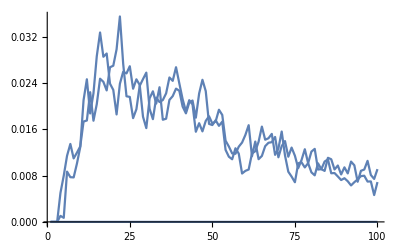

```mathematica
p1 = ListPlot[n[[5,2,All,1]],Joined->True];
p2 = ListPlot[n[[5,2,All,2]],Joined->True];
p3 = ListPlot[n[[5,2,All,3]],Joined->True];
Show[p1,p2,p3,PlotRange->All]
```

```mathematica
totpop
```

{5,{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.},{5.}}